```mathematica
Off[General::"spell1"]
Off[General::"spell"]
SetDirectory["C:\\Users\\Matías\\Documents\\GitHub\\Tesis\\20180821\\Mediciones"];


(*Carga la matriz y determina el período de la señal.*)

Vext=-9000.0;fdbd=1/50.0; fstr=1/50.0;
mat=Import["Bobina 9.csv"];
lm=Length[mat];
V={};Idbd={};Istr={};
Do[AppendTo[V,{mat[[i,4]],mat[[i,5]]}];
AppendTo[Istr,{mat[[i,10]],fdbd*mat[[i,11]]}];AppendTo[Idbd,{mat[[i,16]],fstr*mat[[i,17]]}],{i,1,lm}];
indmax=Floor[N[Mean[Position[V[[All,2]],Max[V[[All,2]]]][[1]]]]];
indmin=Floor[N[Mean[Position[V[[All,2]],Min[V[[All,2]]]]]][[1]]];
tper=Abs[2*(V[[indmax,1]]-V[[indmin,1]])];
iper=Abs[2(indmax-indmin)];

indmaxstr=Floor[N[Mean[Position[V[[All,2]],Max[V[[All,2]]]][[1]]]]];
indminstr=Floor[N[Mean[Position[Istr[[All,2]],Min[Istr[[All,2]]]]]][[1]]];
tperstr=Abs[2*(Istr[[indmaxstr,1]]-Istr[[indminstr,1]])];

(*DEFINIR UN RANGO ALREDEDOR DE INDMAX, TOMAR EL PROMEDIO DE LA DIFERENCIA ENTRE ISTRFIT Y ISTR EN ESE RANGO Y CON ESO DEFINIMOS LA TOLERANCIA AL FIT*)

rangotol={};
Do[AppendTo[rangotol,{indmax+i}],{i,-15,15}];

rangotol


(*indmax=indice para el maximo de tension ; iper=cantidad de elementos en el periodo*)
```

{{543},{544},{545},{546},{547},{548},{549},{550},{551},{552},{553},{554},{555},{556},{557},{558},{559},{560},{561},{562},{563},{564},{565},{566},{567},{568},{569},{570},{571},{572},{573}}

```mathematica
(* Cálculo de potencia y corriente medias de streamers *)
avgpot={};Istrall={};Istravg={};
ninter=100;
lm0=Floor[iper/ninter];minis={};maxis={};
Do[aux=Max[Istr[[(i-1)lm0+1;;i*lm0,2]]];If[aux>0,AppendTo[minis,aux]];aux=Min[Istr[[(i-1)lm0+1;;i*lm0,2]]];If[aux<0,AppendTo[maxis,aux]],{i,1,ninter}];
Iplus=Mean[minis];Imin=Mean[maxis];

Faux=b*Cos[2*Pi/tper*t+c]+d;

Istrfit=Faux/.FindFit[Istr,Faux,{b,c,d},t];

Istraux={};

Do[AppendTo[Istraux,{Istr[[i,1]],Istr[[i,2]]-Istrfit/.t->Istr[[i,1]]}],{i,1,iper}];
(*Do[If[Istr[[i,2]]>Iplus,AppendTo[Istraux,{Istr[[i,1]],Istr[[i,2]]-Iplus}],If[Istr[[i,2]]<Imin,AppendTo[Istraux,{Istr[[i,1]],Istr[[i,2]]-Imin}],AppendTo[Istraux,{Istr[[i,1]],0}]]],{i,1,iper}];*)
Vmax=Max[V[[All,2]]];
Vmin=Min[V[[All,2]]];
Vacm=0.5(Vmax+Vmin);
Vdc=Vacm-Vext;
pot=0.0;Istravg=0.0;
Do[pot+=Istraux[[i,2]]*(V[[i,2]]-Vacm+Vdc);Istravg+=Istr[[i,2]],{i,1,iper}];
avgpot=pot/iper;
Istravg=Istravg/iper;
StringJoin["P media streamers en W: ",ToString[avgpot]]
StringJoin["Corriente media de streamers  en mA : ",ToString[10^3*Istravg]]
```

P media streamers en W: -1.38404

Corriente media de streamers  en mA : 0.0785169

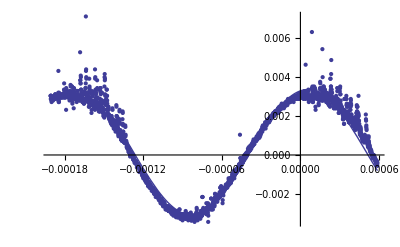

0.000178

```mathematica
Pf=Plot[Istrfit,{t,V[[1,1]],V[[2500,1]]},PlotRange->All];
Poriginal=ListPlot[Istr,PlotRange->All];
Show[Pf,Poriginal]
tper
```

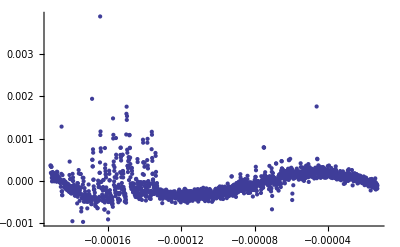

```mathematica
ListPlot[Istraux,PlotRange->All]
```

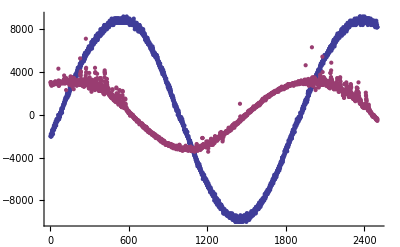

```mathematica
(*Grafica las señales al mismo tiempo*)
Istrcol=Istr[[All,2]];
Vcol=V[[All,2]];



voltaje=ListPlot[{Vcol,10^6*Istrcol}]
(*streamer=ListPlot[Istr]
Show[voltaje,streamer]*)
```

0.00344

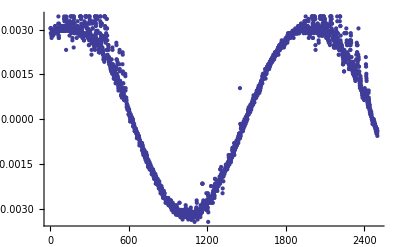

```mathematica
(*Ajuste sobre la funcion recortando los picos de la señal capacitiva*)

Istrrec={};

Corte=Mean[Istr[]



(*Corte=Abs[Min[Istr[[All,2]]]]

Do[If[ Istr[[i,2]]-Istrfit<Corte,AppendTo[Istrrec,{i,Istr[[i,2]]}],AppendTo[Istrrec,{i,Corte}]],{i,1,lm}]

ListPlot[Istrrec]*)

(*EL PROBLEMA ES QUE CORTA BIEN SOLO LOS PICOS DEL MÁXIMO. AL ALEJARSE DE LA CRESTA, YA NO LOS CORTA.
LA IDEA SERIA REALIZAR UN FIT, ESTABLECER UNA TOLERANCIA AL FIT, Y PUNTO A PUNTO RECORTAR LA Istr PARA QUE NO SE PASE DE ESA TOLERANCIA. LUEGO VOLVER A HACER OTRO FIT SOBRE LA FUNCION RECORTADA*)
```

```mathematica
(* Cálculo de potencia y corriente medias de dbd *)
avgpot={};Idbdall={};Idbdavg={};
ninter=300;
lm0=Floor[iper/ninter];minis={};maxis={};
Do[aux=Max[Idbd[[(i-1)lm0+1;;i*lm0,2]]];If[aux>0,AppendTo[minis,aux]];aux=Min[Idbd[[(i-1)lm0+1;;i*lm0,2]]];If[aux<0,AppendTo[maxis,aux]],{i,1,ninter}];
Iplus=Mean[minis];Imin=Mean[maxis];
Idbdaux={};
Do[If[Idbd[[i,2]]>Iplus,AppendTo[Idbdaux,{Idbd[[i,1]],Idbd[[i,2]]-Iplus}],If[Idbd[[i,2]]<Imin,AppendTo[Idbdaux,{Idbd[[i,1]],Idbd[[i,2]]-Imin}],AppendTo[Idbdaux,{Idbd[[i,1]],0}]]],{i,1,iper}];
Vmax=Max[V[[All,2]]];
Vmin=Min[V[[All,2]]];
Vacm=0.5(Vmax+Vmin);
Vdc=Vacm-Vext;
pot=0.0;Idbdavg=0.0;
Do[pot+=Idbdaux[[i,2]]*(V[[i,2]]-Vacm);Idbdavg+=Idbd[[i,2]],{i,1,iper}];
avgpot=pot/iper;
Idbdavg=Idbdavg/iper;
StringJoin["P media de DBD en W: ",ToString[avgpot]]
StringJoin["Corriente media de DBD  en mA : ",ToString[10^3*Idbdavg]]
```

P media de DBD en W: 5.37364

Corriente media de DBD  en mA : 20.5933

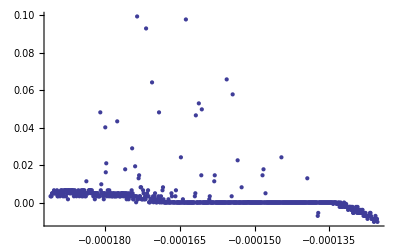

```mathematica
ListPlot[Idbdaux,PlotRange->All]
```

```mathematica
1/tper
```

13513.5

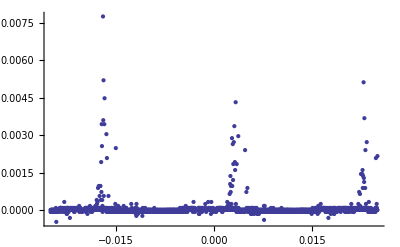

```mathematica
ListPlot[Istr,PlotRange->All]
```

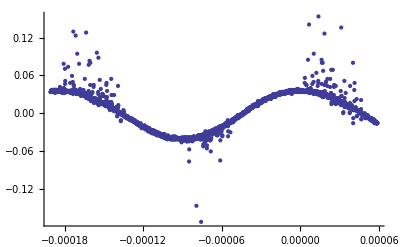

```mathematica
ListPlot[Idbd,PlotRange->All]
```

```mathematica
indmin
indmax
V[[indmin,2]]
V[[indmax,2]]
```

1448

1777

-9800.

-4400.